1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {omega, CDM candidate name, Xf}, self explanatory

6) {cross section in pb, input channel, output channel}, cross sections for selected channels

7) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}
 
 8) Bsgamma ect
 
 9) {{Δa_e, Δa_μ, Δa_τ},
 {d_e, d_μ, d_τ}, 
 {BR( τ -> μ γ ), BR( τ -> e γ ), BR( μ -> e γ ) }}

```mathematica
(* NMP5 *)
file5c=<<"/Users/ruppell/Math/temp/NMP5_cpc_clean.txt";
label5c="NMP5 CPC";
file5v=<<"/Users/ruppell/Math/temp/NMP5_cpv_clean.txt"; 
label5v="NMP5 CPV";

(* NMP9 *)
file9c=<<"/Users/ruppell/Math/temp/NMP9_cpc_clean.txt";
label9c="NMP9 CPC";
file9v=<<"/Users/ruppell/Math/temp/NMP9_cpv_clean.txt"; 
label9v="NMP9 CPV";

yesCPsnuLSP[name_String]:=Select[ToExpression[name<>"v"],#[[3,5,1]]<Abs@#[[3,1,1]]&];
yesCPχ0LSP[name_String]:=Select[ToExpression[name<>"v"],#[[3,5,1]]>Abs@#[[3,1,1]]&];
noCPsnuLSP[name_String]:=Select[ToExpression[name<>"c"],#[[3,5,1]]<Abs@#[[3,1,1]]&];
noCPχ0LSP[name_String]:=Select[ToExpression[name<>"c"],#[[3,5,1]]>Abs@#[[3,1,1]]&];
```

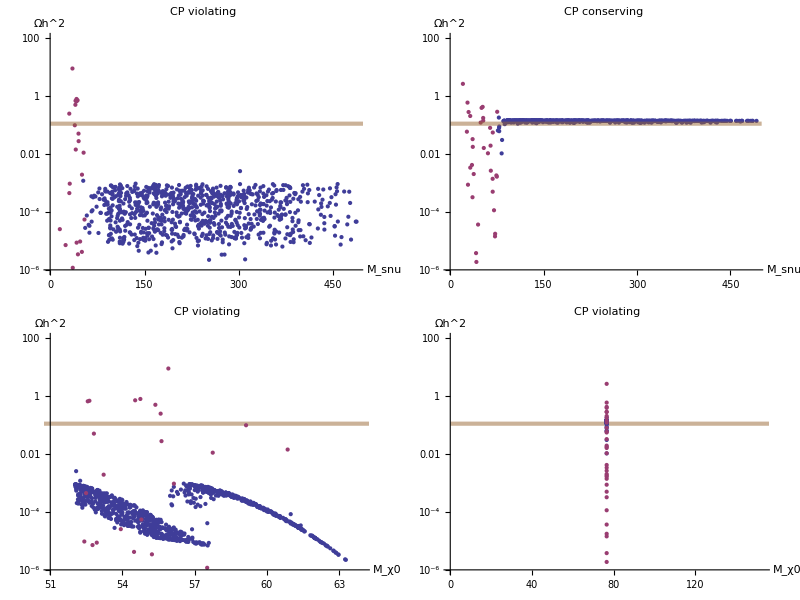

```mathematica
file1=yesCPχ0LSP["file5"];
file2=yesCPsnuLSP["file5"];
file3=noCPχ0LSP["file5"];
file4=noCPsnuLSP["file5"];
p1=Show[
ListLogPlot[{Transpose@{file1[[;;,3,5,1]],file1[[;;,5,1]]},Transpose@{file2[[;;,3,5,1]],file2[[;;,5,1]]}},AxesLabel->{"M_snu","Ωh^2"},ImageSize->400,PlotLabel->"CP violating",PlotRange->{Automatic,{10^-6,100}}],
Graphics@{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
p2=Show[
ListLogPlot[{Transpose@{file3[[;;,3,5,1]],file3[[;;,5,1]]},Transpose@{file4[[;;,3,5,1]],file4[[;;,5,1]]}},AxesLabel->{"M_snu","Ωh^2"},ImageSize->400,PlotLabel->"CP conserving",PlotRange->{Automatic,{10^-6,100}}],
Graphics@{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
p3=ListLogPlot[{Transpose@{Abs@file1[[;;,3,1,1]],file1[[;;,5,1]]},Transpose@{Abs@file2[[;;,3,1,1]],file2[[;;,5,1]]}},AxesLabel->{"M_χ0","Ωh^2"},ImageSize->400,PlotLabel->"CP violating",PlotRange->{{51,64},{10^-6,100}},Prolog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
p4=ListLogPlot[{Transpose@{Abs@file3[[;;,3,1,1]],file3[[;;,5,1]]},Transpose@{Abs@file4[[;;,3,1,1]],file4[[;;,5,1]]}},AxesLabel->{"M_χ0","Ωh^2"},ImageSize->400,PlotLabel->"CP violating",PlotRange->{Automatic,{10^-6,100}},Prolog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
TableForm@{{p1,p2},{p3,p4}}
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/NMP5cpv.eps",p1,"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/NMP5cpc.eps",p2,"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/NMP5_Mchi0.eps",p3,"EPS"];
```

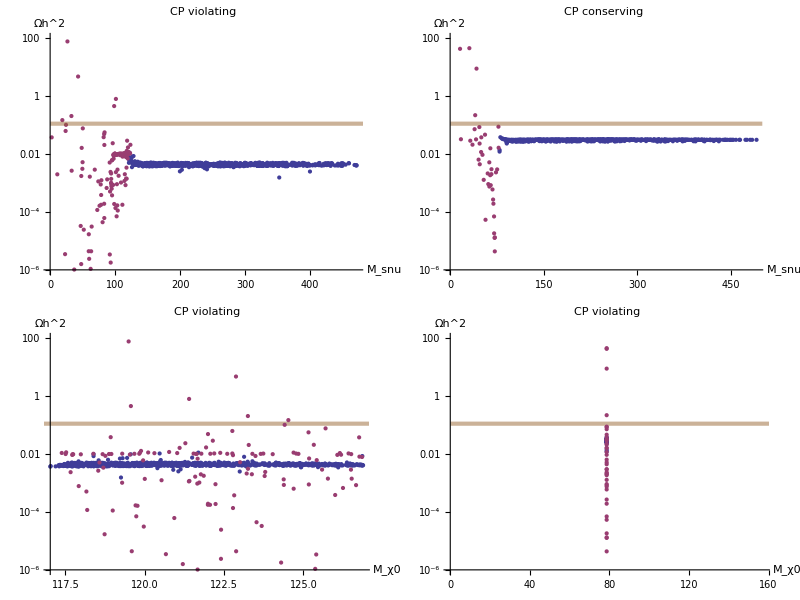

```mathematica
file1=yesCPχ0LSP["file9"];
file2=yesCPsnuLSP["file9"];
file3=noCPχ0LSP["file9"];
file4=noCPsnuLSP["file9"];
p1=Show[
ListLogPlot[{Transpose@{Abs@file1[[;;,3,5,1]],file1[[;;,5,1]]},Transpose@{file2[[;;,3,5,1]],file2[[;;,5,1]]}},AxesLabel->{"M_snu","Ωh^2"},ImageSize->400,PlotLabel->"CP violating",PlotRange->{Automatic,{10^-6,100}}],
Graphics@{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
p2=Show[
ListLogPlot[{Transpose@{file3[[;;,3,5,1]],file3[[;;,5,1]]},Transpose@{file4[[;;,3,5,1]],file4[[;;,5,1]]}},AxesLabel->{"M_snu","Ωh^2"},ImageSize->400,PlotLabel->"CP conserving",PlotRange->{Automatic,{10^-6,100}}],
Graphics@{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
p3=ListLogPlot[{Transpose@{Abs@file1[[;;,3,1,1]],file1[[;;,5,1]]},Transpose@{Abs@file2[[;;,3,1,1]],file2[[;;,5,1]]}},AxesLabel->{"M_χ0","Ωh^2"},ImageSize->400,PlotLabel->"CP violating",PlotRange->{Automatic,{10^-6,100}},Prolog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
p4=ListLogPlot[{Transpose@{Abs@file3[[;;,3,1,1]],file3[[;;,5,1]]},Transpose@{Abs@file4[[;;,3,1,1]],file4[[;;,5,1]]}},AxesLabel->{"M_χ0","Ωh^2"},ImageSize->400,PlotLabel->"CP violating",PlotRange->{Automatic,{10^-6,100}},Prolog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}];
TableForm@{{p1,p2},{p3,p4}}
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/NMP9cpv.eps",p1,"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/NMP9cpc.eps",p2,"EPS"];
```

```mathematica
Block[{a5c,a5v,a9c,a9v,assign,file,out,range,foo,h1max,h1min,h2max,h2min,h3max,h3min,h4max,h4min,h5max,h5min,hCmax,hCmin,sbtmax,sbtmin,sdnmax,sdnmin,sl1max,sl1min,sl2max,sl2min,sl3max,sl3min,sl4max,sl4min,sl5max,sl5min,sl6max,sl6min,snuLmax,snuLmin,snuRmax,snuRmin,stpmax,stpmin,supmax,supmin,zero,nuRmax,nuRmin,c01max,c01min,c02max,c02min,c03max,c03min,c04max,c04min,c05max,c05min,cC1max,cC1min,cC2max,cC2min},
assign[name_]:={{{c01min,c01max},{c02min,c02max},{c03min,c03max},{c04min,c04max},{c05min,c05max}},
{{cC1min,cC1max},{cC2min,cC2max}},
{{zero,zero},{hCmin,hCmax}},
{{zero,zero},{zero,zero},{zero,zero},{nuRmin,nuRmax}},
{{snuRmin,foo},{foo,foo},{snuLmin,snuLmax},{foo,foo},{foo,foo},{foo,foo},{foo,foo},{foo,snuRmax}},
{{zero,zero},{h1min,h1max},{h2min,h2max},{h3min,h3max},{h4min,h4max},{h5min,h5max}},
{{sl1min,sl1max},{sl2min,sl2max},{sl3min,sl3max},{sl4min,sl4max},{sl5min,sl5max},{sl6min,sl6max}},
{{supmin,foo},{foo,supmax}},
{{sdnmin,foo},{foo,sdnmax}},
{{stpmin,foo},{foo,stpmax}},
{{sbtmin,foo},{foo,sbtmax}}}=({Round@Min@#,Round@Max@#}&/@Transpose@Abs@name[[;;,3,#]])&/@Range@11;
a5c:=assign[file5c];
a5v:=assign[file5v];
a9c:=assign[file9c];
a9v:=assign[file9v];
range=If[Abs[#[[1]]-#[[2]]]<3,ToString@#[[1]]<>"GeV",ToString@#[[1]]<>"--"<>ToString@#[[2]]<>"GeV"]&;
file = "/Users/ruppell/Math/temp/Spectrum.mc";
out=OpenWrite[file];
Write[out,OutputForm["\\begin{table}"]];
Write[out,OutputForm["\\bc"]];
Write[out,OutputForm["\\bt{|c|ccccc|}"]];
Write[out,OutputForm["\\hline"]];

Write[out,OutputForm["\\mc{6}{|c|}{NMP5 CP conserving}\\\\\\hline"]];
Write[out,OutputForm["$\\chi^0$&<* a5c;range@{c01min,c01max} *>&<* range@{c02min,c02max} *>&<* range@{c03min,c03max} *>"]];
Write[out,OutputForm["&<* range@{c04min,c04max} *>&<* range@{c05min,c05max} *>\\\\"]];
Write[out,OutputForm["$\\chi^\\pm$&<* range@{cC1min,cC1max} *>&<* range@{cC2min,cC2max} *>&&&\\\\"]];
Write[out,OutputForm["$h^0_i$&<* range@{h1min,h1max} *>&<* range@{h2min,h2max} *>&<* range@{h3min,h3max} *>"]];
Write[out,OutputForm["&<* range@{h4min,h4max} *>&<* range@{h5min,h5max} *>\\\\"]];
Write[out,OutputForm["$h^\\pm$&<* range@{hCmin,hCmax} *>&&&&\\\\\\hline"]];
(**)
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["\\mc{6}{|c|}{NMP5 CP violating}\\\\\\hline"]];
Write[out,OutputForm["$\\chi^0$&<* a5v;range@{c01min,c01max} *>&<* range@{c02min,c02max} *>&<* range@{c03min,c03max} *>"]];
Write[out,OutputForm["&<* range@{c04min,c04max} *>&<* range@{c05min,c05max} *>\\\\"]];
Write[out,OutputForm["$\\chi^\\pm$&<* range@{cC1min,cC1max} *>&<* range@{cC2min,cC2max} *>&&&\\\\"]];
Write[out,OutputForm["$h^0_i$&<* range@{h1min,h1max} *>&<* range@{h2min,h2max} *>&<* range@{h3min,h3max} *>"]];
Write[out,OutputForm["&<* range@{h4min,h4max} *>&<* range@{h5min,h5max} *>\\\\"]];
Write[out,OutputForm["$h^\\pm$&<* range@{hCmin,hCmax} *>&&&&\\\\\\hline"]];
(**)
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["\\mc{6}{|c|}{NMP9 CP conserving}\\\\\\hline"]];
Write[out,OutputForm["$\\chi^0$&<* a9c;range@{c01min,c01max} *>&<* range@{c02min,c02max} *>&<* range@{c03min,c03max} *>"]];
Write[out,OutputForm["&<* range@{c04min,c04max} *>&<* range@{c05min,c05max} *>\\\\"]];
Write[out,OutputForm["$\\chi^\\pm$&<* range@{cC1min,cC1max} *>&<* range@{cC2min,cC2max} *>&&&\\\\"]];
Write[out,OutputForm["$h^0_i$&<* range@{h1min,h1max} *>&<* range@{h2min,h2max} *>&<* range@{h3min,h3max} *>"]];
Write[out,OutputForm["&<* range@{h4min,h4max} *>&<* range@{h5min,h5max} *>\\\\"]];
Write[out,OutputForm["$h^\\pm$&<* range@{hCmin,hCmax} *>&&&&\\\\\\hline"]];
(**)
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["\\mc{6}{|c|}{NMP9 CP violating}\\\\\\hline"]];
Write[out,OutputForm["$\\chi^0$&<* a9v;range@{c01min,c01max} *>&<* range@{c02min,c02max} *>&<* range@{c03min,c03max} *>"]];
Write[out,OutputForm["&<* range@{c04min,c04max} *>&<* range@{c05min,c05max} *>\\\\"]];
Write[out,OutputForm["$\\chi^\\pm$&<* range@{cC1min,cC1max} *>&<* range@{cC2min,cC2max} *>&&&\\\\"]];
Write[out,OutputForm["$h^0_i$&<* range@{h1min,h1max} *>&<* range@{h2min,h2max} *>&<* range@{h3min,h3max} *>"]];
Write[out,OutputForm["&<* range@{h4min,h4max} *>&<* range@{h5min,h5max} *>\\\\"]];
Write[out,OutputForm["$h^\\pm$&<* range@{hCmin,hCmax} *>&&&&\\\\\\hline"]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\caption{\\label{tab:chimass}The neutralino, chargino, natural higgs"]];
Write[out,OutputForm[" and charged higgs masses / mass ranges for the four scenarios.}"]];
Write[out,OutputForm["\\ec"]];
Write[out,OutputForm["\\end{table}"]];
(**)
Write[out,OutputForm["\\begin{table}"]];
Write[out,OutputForm["\\bc"]];
Write[out,OutputForm["\\bt{|c|c|c|c|c|}"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["&NMP5 CPc&NMP5 CPv&NMP9 CPc&NMP9 CPv\\\\\\hline"]];
Write[out,OutputForm["$h^\\pm$&<* assign[file5c];range@{hCmin,hCmax} *>&<* assign[file5v];range@{hCmin,hCmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{hCmin,hCmax} *>&<* assign[file9v];range@{hCmin,hCmax} *>\\\\"]];
Write[out,OutputForm["$\\nu_R$&<* assign[file5c];range@{nuRmin,nuRmax} *>&<* assign[file5v];range@{nuRmin,nuRmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{nuRmin,nuRmax} *>&<* assign[file9v];range@{nuRmin,nuRmax} *>\\\\\\hline"]];
Write[out,OutputForm["$\\tilde\\nu_R$&<* assign[file5c];range@{snuRmin,snuRmax} *>&<* assign[file5v];range@{snuRmin,snuRmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{snuRmin,snuRmax} *>&<* assign[file9v];range@{snuRmin,snuRmax} *>\\\\"]];
Write[out,OutputForm["$\\tilde\\nu_L$&<* assign[file5c];range@{snuLmin,snuLmax} *>&<* assign[file5v];range@{snuLmin,snuLmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{snuLmin,snuLmax} *>&<* assign[file9v];range@{snuLmin,snuLmax} *>\\\\"]];
Write[out,OutputForm["$\\tilde{l}$&<* assign[file5c];range@{sl1min,sl6max} *>&<* assign[file5v];range@{sl1min,sl6max} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{sl1min,sl6max} *>&<* assign[file9v];range@{sl1min,sl6max} *>\\\\\\hline"]];
Write[out,OutputForm["$\\tilde{u}$&<* assign[file5c];range@{supmin,supmax} *>&<* assign[file5v];range@{supmin,supmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{supmin,supmax} *>&<* assign[file9v];range@{supmin,supmax} *>\\\\"]];
Write[out,OutputForm["$\\tilde{d}$&<* assign[file5c];range@{sdnmin,sdnmax} *>&<* assign[file5v];range@{sdnmin,sdnmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{sdnmin,sdnmax} *>&<* assign[file9v];range@{sdnmin,sdnmax} *>\\\\"]];
Write[out,OutputForm["$\\tilde{t}$&<* assign[file5c];range@{stpmin,stpmax} *>&<* assign[file5v];range@{stpmin,stpmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{stpmin,stpmax} *>&<* assign[file9v];range@{stpmin,stpmax} *>\\\\"]];
Write[out,OutputForm["$\\tilde{b}$&<* assign[file5c];range@{sbtmin,sbtmax} *>&<* assign[file5v];range@{sbtmin,sbtmax} *>&"]];Write[out,OutputForm["<* assign[file9c];range@{sbtmin,sbtmax} *>&<* assign[file9v];range@{sbtmin,sbtmax} *>\\\\\\hline"]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\caption{\\label{tab:allmass}The mass ranges of particles not listed in table \\ref{tab:chimass}.}"]];
Write[out,OutputForm["\\ec"]];
Write[out,OutputForm["\\end{table}"]];
Close[file];
Splice[file,PageWidth->Infinity];
DeleteFile[file];
]
```

```mathematica
TableForm@{
{MatrixForm@(Abs@#[[1,3,1]])&[file5c]MatrixForm@Chop[Power[Abs@(#[[1,4,1]]+I#[[1,4,2]]),2],0.05]&[file5c],
MatrixForm@(Abs@#[[1,3,1]])&[file5v]MatrixForm@Chop[Power[Abs@(#[[1,4,1]]+I#[[1,4,2]]),2],0.05]&[file5v]},
{MatrixForm@(Abs@#[[1,3,1]])&[file9c]MatrixForm@Chop[Power[Abs@(#[[1,4,1]]+I#[[1,4,2]]),2],0.05]&[file9c],
MatrixForm@(Abs@#[[1,3,1]])&[file9v]MatrixForm@Chop[Power[Abs@(#[[1,4,1]]+I#[[1,4,2]]),2],0.05]&[file9v]}}
```

(76.5562
173.909
233.475
237.243
426.03) (0 | 0 | 0 | 0.275573 | 0.64705
0.461554 | 0 | 0.251426 | 0.0663887 | 0.200192
0.495639 | 0.0666012 | 0.220027 | 0.166819 | 0.0509134
0 | 0 | 0.471527 | 0.423453 | 0.100863
0 | 0.892197 | 0 | 0.0677665 | 0) | (52.2157
165.283
230.104
255.354
424.503) (0 | 0 | 0 | 0.248606 | 0.714754
0.430947 | 0 | 0.324735 | 0.16082 | 0.0515322
0.556588 | 0.0584137 | 0.193393 | 0.177173 | 0
0 | 0 | 0.429089 | 0.34869 | 0.218772
0 | 0.900709 | 0 | 0.0647114 | 0)
(78.6198
143.45
180.013
235.83
286.393) (0.210945 | 0.151339 | 0.12007 | 0.255095 | 0.262553
0.725495 | 0.0538727 | 0 | 0 | 0.185051
0 | 0.416193 | 0.139784 | 0 | 0.417338
0 | 0 | 0.471786 | 0.437151 | 0.0830039
0 | 0.372902 | 0.266973 | 0.271553 | 0.0520547) | (117.898
135.303
180.002
249.747
264.233) (0.0726396 | 0 | 0 | 0.272996 | 0.609694
0.858807 | 0 | 0.0558905 | 0 | 0.0772506
0 | 0.582747 | 0.245477 | 0.0771999 | 0.0591292
0 | 0 | 0.444685 | 0.312006 | 0.227428
0 | 0.378962 | 0.235931 | 0.329822 | 0)

```mathematica
(* BM hS noCPV χ0-LSP *)
bench1=<<"/Users/ruppell/Math/temp/BME_hS-noCP-chi0LSP-2392_clean.txt";
label1="hS noCPV χ0-LSP";
(* BM hS noCPV snu-LSP *)
bench2=<<"/Users/ruppell/Math/temp/BME_hS-noCP-snuLSP-83_clean.txt";
label2="hS noCPV snu-LSP";
(* BM hS yesCPV χ0-LSP *)
bench3=<<"/Users/ruppell/Math/temp/BME_hS-yesCP-chi0LSP-2011_clean.txt";
label3="hS yesCPV χ0-LSP";
(* BM hS yesCPV snu-LSP *)
bench4=<<"/Users/ruppell/Math/temp/BME_hS-yesCP-snuLSP-729_clean.txt";
label4="hS yesCPV snu-LSP";
(* BM hSM noCPV χ0-LSP *)
bench5=<<"/Users/ruppell/Math/temp/BME_hSM-noCP-chi0LSP-2557_clean.txt";
label5="hSM noCPV χ0-LSP";
(* BM hSM noCPV snu-LSP *)
bench6=<<"/Users/ruppell/Math/temp/BME_hSM-noCP-snuLSP-47_clean.txt";
label6="hSM noCPV snu-LSP";
(* BM hSM yesCPV χ0-LSP *)
bench7=<<"/Users/ruppell/Math/temp/BME_hSM-yesCP-chi0LSP-2048_clean.txt";
label7="hSM yesCPV χ0-LSP";
(* BM hSM yesCPV snu-LSP *)
bench8=<<"/Users/ruppell/Math/temp/BME_hSM-yesCP-snuLSP-2619_clean.txt";
label8="hSM yesCPV snu-LSP";
```

```mathematica
plot5=ListPlot[
Transpose@{Log[10,#1[[;;,5,1]]],Log[10,Abs@#1[[;;,##2]]]},
AxesOrigin->{-5,-24.5},
AspectRatio->1,
ImageSize->400,
PlotRange->{{0,-5},{-24.5,-28}},
Prolog->{
{Opacity[0.5,LightBrown],Rectangle[{10~Log~0.0941,-24.5},{10~Log~0.1311,-28}]},
{Opacity[0.5,LightBrown],Rectangle[{-5,10~Log~14.3*^-28},{0,-28}]},
{Thin,Line@{{-5,10~Log~14.3*^-28},{0,10~Log~14.3*^-28}}},
{Thin,Line@{{10~Log~0.0941,-24.5},{10~Log~0.0941,-28}}},
{Thin,Line@{{10~Log~0.1311,-24.5},{10~Log~0.1311,-28}}}}
]&[#,9,2,1]&;
plot6=ListPlot[
Transpose@{Log[10,#1[[;;,6,1]]],Log[10,Abs@#1[[;;,##2]]]},
AxesOrigin->{-5,-24.5},
AspectRatio->1,
ImageSize->400,
PlotRange->{{0,-5},{-24.5,-28}},
Prolog->{
{Opacity[0.5,LightBrown],Rectangle[{10~Log~0.0941,-24.5},{10~Log~0.1311,-28}]},
{Opacity[0.5,LightBrown],Rectangle[{-5,10~Log~14.3*^-28},{0,-28}]},
{Thin,Line@{{-5,10~Log~14.3*^-28},{0,10~Log~14.3*^-28}}},
{Thin,Line@{{10~Log~0.0941,-24.5},{10~Log~0.0941,-28}}},
{Thin,Line@{{10~Log~0.1311,-24.5},{10~Log~0.1311,-28}}}}
]&[#,10,2,1]&;
```

```mathematica
Dimensions/@{bench1,bench2,bench3,bench4,bench5,bench6,bench7,bench8}
```

{{963,9},{949,10},{804,9},{958,9},{985,9},{983,10},{988,9},{991,9}}

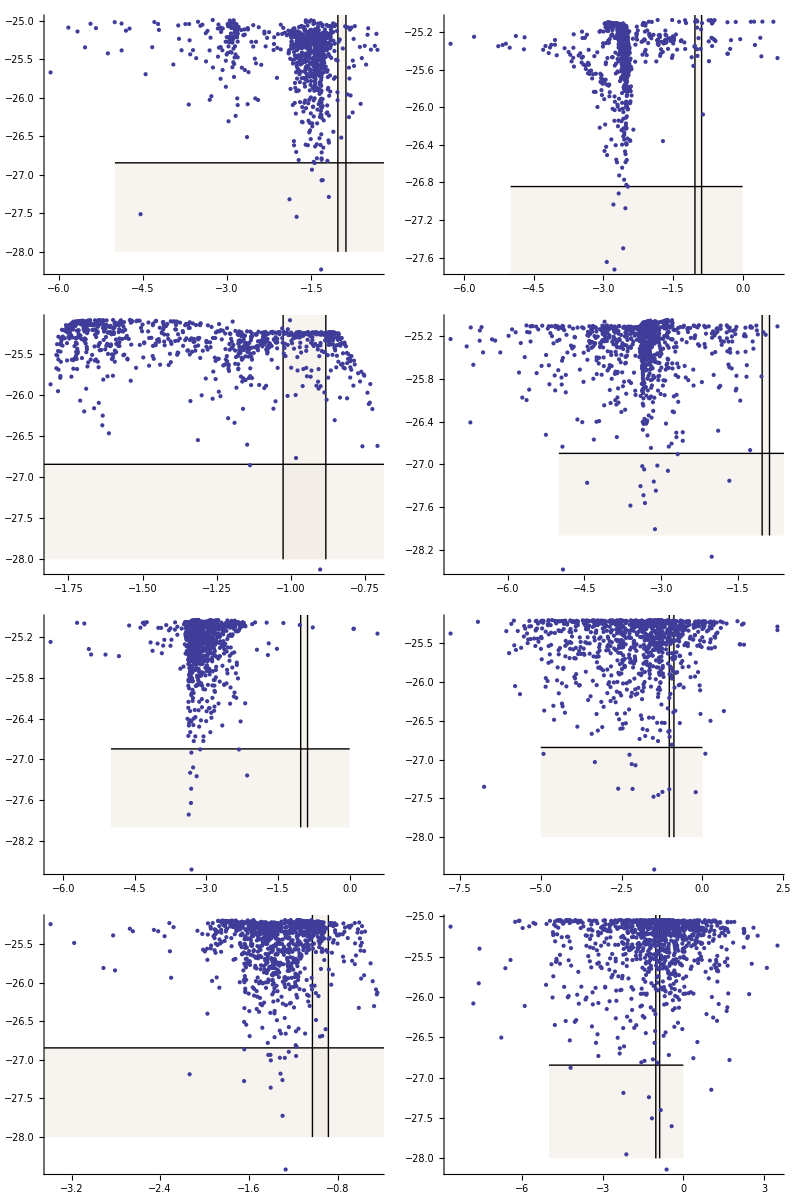

```mathematica
TableForm@{{plot5@bench1,plot6@bench2},{plot5@bench3,plot5@bench4},{plot5@bench5,plot6@bench6},{plot5@bench7,plot5@bench8}}
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label1,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench1],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label2,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench2],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label3,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench3],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label4,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench4],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label5,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench5],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label6,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench6],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label7,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench7],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label8,{" "->"","χ"->"chi","-"->""}]<>".eps",plot[bench8],"EPS"];
```

```mathematica
TableForm@Transpose@{ {"par","M1","M2","M3","M0","Mtau","MQ","MNR","tanβ","v","vevS","Atop","Abtm","Atau","An11","An12","An13","AlambdaN","Yn11","Yn12","Yn13","lambda","lambdaN","kappa","PhisPI","Phi2PI","ksi","Alambda","Akappa","mh1","mh2","mS"},
{label1}~Join~N@bench1[[1,2]],
{label2}~Join~N@bench2[[1,2]],
{label3}~Join~N@bench3[[1,2]],
{label4}~Join~N@bench4[[1,2]],
{label5}~Join~N@bench5[[1,2]],
{label6}~Join~N@bench6[[1,2]],
{label7}~Join~N@bench7[[1,2]],
{label8}~Join~N@bench8[[1,2]]}
```

par | hS noCPV χ0-LSP | hS noCPV snu-LSP | hS yesCPV χ0-LSP | hS yesCPV snu-LSP | hSM noCPV χ0-LSP | hSM noCPV snu-LSP | hSM yesCPV χ0-LSP | hSM yesCPV snu-LSP
M1 | 300. | 300. | 300. | 300. | 300. | 300. | 300. | 300.
M2 | 600. | 600. | 600. | 600. | 600. | 600. | 600. | 600.
M3 | 1800. | 1800. | 1800. | 1800. | 1800. | 1800. | 1800. | 1800.
M0 | 310. | 425. | 450. | 285. | 300. | 460. | 400. | 240.
Mtau | 1.77 | 1.77 | 1.77 | 1.77 | 1.77 | 1.77 | 1.77 | 1.77
MQ | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000.
MNR | 200. | 195. | 500. | 40. | 400. | 230. | 390. | 160.
tanβ | 42. | 32. | 30. | 39. | 4. | 35. | 10. | 5.
v | 174. | 174. | 174. | 174. | 174. | 174. | 174. | 174.
vevS | 1250. | 386.667 | 560. | 578.431 | 1500. | 729.167 | 787.037 | 1212.12
Atop | 1500. | 1500. | 1500. | 1500. | 1500. | 1500. | 1500. | 1500.
Abtm | 1500. | 1500. | 1500. | 1500. | 1500. | 1500. | 1500. | 1500.
Atau | -2500. | -2500. | -2500. | -2500. | -2500. | -2500. | -2500. | -2500.
An11 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
An12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
An13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
AlambdaN | -280. | -330. | -45. | 220. | -700. | -100. | 700. | 580.
Yn11 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6
Yn12 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6
Yn13 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6 | 1.×10^-6
lambda | 0.32 | 0.75 | 0.75 | 0.51 | 0.12 | 0.48 | 0.54 | 0.33
lambdaN | 0.25 | 0.17 | 0.48 | 0.38 | 0.28 | 0.15 | 0.73 | 0.12
kappa | 0.26 | 0.77 | 0.6 | 0.6 | 0.45 | 0.7 | 0.56 | 0.74
PhisPI | 5.84692 | 5.94324 | 5.97257 | 4.85776 | 5.90571 | 4.46971 | 0.223764 | 5.16709
Phi2PI | 5.37053 | 5.15163 | 3.58396 | 3.34822 | 5.21983 | 3.04033 | 2.11599 | 4.14197
ksi | -462.579 | -451.851 | -329.959 | 275.19 | -634.867 | -520.274 | -762.317 | 89.0458
Alambda | -13.8573 | -131.116 | -2236.24 | 30.5463 | -207.187 | -203.68 | -610.9 | -706.352
Akappa | 106.57 | 310.787 | 68.2849 | 113.513 | 102.304 | -492.905 | 445.743 | 0.737505
mh1 | 2300.87 | 1515.25 | 5069.94 | 1950.7 | 644.292 | 2205.68 | 1199.42 | 1740.71
mh2 | 0.+361.416 ⅈ | 0.+235.541 ⅈ | 0.+348.364 ⅈ | 0.+241.214 ⅈ | 154.924 | 0.+303.537 ⅈ | 0.+371.291 ⅈ | 0.+69.5551 ⅈ
mS | 0.+389.144 ⅈ | 0.+129.878 ⅈ | 0.+439.173 ⅈ | 0.+486.71 ⅈ | 0.+884.137 ⅈ | 0.+637.598 ⅈ | 0.+40.3183 ⅈ | 0.+1268.1 ⅈ

```mathematica
Block[{file,out,range,b1,b2,b3,b4,b5,b6,b7,b8,assign,M1,M2,M3,M0,Mtau,MQ,MNR,tanb,v,vevS,Atop,Abtm,Atau,An11,An12,An13,AlambdaN,Yn11,Yn12,Yn13,lambda,lambdaN,kappa,PhisPI,Phi2PI,ksi,Alambda,Akappa,mh1,mh2,ms},
assign[name_]:={M1,M2,M3,M0,Mtau,MQ,MNR,tanb,v,vevS,Atop,Abtm,Atau,An11,An12,An13,AlambdaN,Yn11,Yn12,Yn13,lambda,lambdaN,kappa,PhisPI,Phi2PI,ksi,Alambda,Akappa,mh1,mh2,ms}=name[[1,2]];
b1:=assign[bench1];
b2:=assign[bench2];
b3:=assign[bench3];
b4:=assign[bench4];
b5:=assign[bench5];
b6:=assign[bench6];
b7:=assign[bench7];
b8:=assign[bench8];
range=If[Abs[#[[1]]-#[[2]]]<3,ToString@#[[1]]<>"GeV",ToString@#[[1]]<>"--"<>ToString@#[[2]]<>"GeV"]&;
file = "/Users/ruppell/Math/temp/Parameters.mc";
out=OpenWrite[file];
Write[out,OutputForm["\\begin{table}"]];
Write[out,OutputForm["\\bc"]];
Write[out,OutputForm["\\bt{|c|c|}"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$M_1$&<* b1;M1 *> GeV \\\\"]];
Write[out,OutputForm["$M_2$&<* M2 *> GeV \\\\"]];
Write[out,OutputForm["$M_3$&<* M3 *> GeV \\\\\\hline"]];
Write[out,OutputForm["$M_\\tau$&<* Mtau *> GeV \\\\"]];
Write[out,OutputForm["$M_Q$&<* MQ *> GeV \\\\\\hline"]];
Write[out,OutputForm["$A_t$&<* Atop *> GeV \\\\"]];
Write[out,OutputForm["$A_b$&<* Abtm *> GeV \\\\"]];
Write[out,OutputForm["$A_\\tau$&<* Atau *> GeV \\\\\\hline"]];
Write[out,OutputForm["$Y_{N_i}$&<* Yn11 *>\\\\"]];
Write[out,OutputForm["$A_{N_i}$&<* An11 *> GeV \\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\caption{\\label{tab:parCommon}The parameters that"]];
Write[out,OutputForm[" all benchmark points have in common.}"]];
Write[out,OutputForm["\\ec"]];
Write[out,OutputForm["\\end{table}"]];
(**)
Write[out,OutputForm["\\begin{table}"]];
Write[out,OutputForm["\\bc"]];
Write[out,OutputForm["\\bt{|c|c|c|c|c|c|c|c|c|}"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$h^0_1$&\\mc{4}{c|}{Singlet like}&\\mc{4}{c|}{SM like}\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["CP&\\mc{2}{c|}{cons}&\\mc{2}{c|}{viol}&\\mc{2}{c|}{cons}&\\mc{2}{c|}{viol}\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["LSP&$\\chi^0_1$&$\\tilde\\nu$&$\\chi^0_1$&$\\tilde\\nu$"]];
Write[out,OutputForm["&$\\chi^0_1$&$\\tilde\\nu$&$\\chi^0_1$&$\\tilde\\nu$\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$\\tan\\beta$&<* b1;tanb *>&<* b2;tanb *>&<* b3;tanb *>&<* b4;tanb *>"]];
Write[out,OutputForm["&<* b5;tanb *>&<* b6;tanb *>&<* b7;tanb *>&<* b8;tanb *>\\\\"]];
Write[out,OutputForm["$\\mu$&<* b1;Round[lambda*vevS] *>&<* b2;Round[lambda*vevS] *>"]];
Write[out,OutputForm["&<* b3;Round[lambda*vevS] *>&<* b4;Round[lambda*vevS] *>"]];
Write[out,OutputForm["&<* b5;Round[lambda*vevS] *>&<* b6;Round[lambda*vevS] *>"]];
Write[out,OutputForm["&<* b7;Round[lambda*vevS] *>&<* b8;Round[lambda*vevS] *>\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$\\lambda$&<* b1;lambda *>&<* b2;lambda *>&<* b3;lambda *>&<* b4;lambda *>"]];
Write[out,OutputForm["&<* b5;lambda *>&<* b6;lambda *>&<* b7;lambda *>&<* b8;lambda *>\\\\"]];
Write[out,OutputForm["$\\kappa$&<* b1;kappa *>&<* b2;kappa *>&<* b3;kappa *>&<* b4;kappa *>"]];
Write[out,OutputForm["&<* b5;kappa *>&<* b6;kappa *>&<* b7;kappa *>&<* b8;kappa *>\\\\"]];
Write[out,OutputForm["$\\lambda_N$&<* b1;lambdaN *>&<* b2;lambdaN *>"]];
Write[out,OutputForm["&<* b3;lambdaN *>&<* b4;lambdaN *>"]];
Write[out,OutputForm["&<* b5;lambdaN *>&<* b6;lambdaN *>"]];
Write[out,OutputForm["&<* b7;lambdaN *>&<* b8;lambdaN *>\\\\"]];
Write[out,OutputForm["$A_{\\lambda_N}$&<* b1;AlambdaN *>&<* b2;AlambdaN *>"]];
Write[out,OutputForm["&<* b3;AlambdaN *>&<* b4;AlambdaN *>"]];
Write[out,OutputForm["&<* b5;AlambdaN *>&<* b6;AlambdaN *>"]];
Write[out,OutputForm["&<* b7;AlambdaN *>&<* b8;AlambdaN *>\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$M_0$&<* b1;M0 *>&<* b2;M0 *>&<* b3;M0 *>&<* b4;M0 *>"]];
Write[out,OutputForm["&<* b5;M0 *>&<* b6;M0 *>&<* b7;M0 *>&<* b8;M0 *>\\\\"]];
Write[out,OutputForm["$M_{N_R}$&<* b1;MNR *>&<* b2;MNR *>&<* b3;MNR *>&<* b4;MNR *>"]];
Write[out,OutputForm["&<* b5;MNR *>&<* b6;MNR *>&<* b7;MNR *>&<* b8;MNR *>\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["Bench&\\#1&\\#2&\\#3&\\#4&\\#5&\\#6&\\#7&\\#8\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\caption{\\label{tab:par}The parameters for our benchmark points.}"]];
Write[out,OutputForm["\\ec"]];
Write[out,OutputForm["\\end{table}"]];
Close[file];
Splice[file,PageWidth->Infinity];
DeleteFile[file];
]
```

```mathematica
Block[{file,out,range,mb1,mb2,mb3,mb4,mb5,mb6,mb7,mb8,ab1,ab2,ab3,ab4,ab5,ab6,ab7,ab8,assignM,assignA,almin,almax,akmin,akmax,msmin,msmax,mh2min,mh2max,mh1min,mh1max},assignM[name_]:={{msmin,msmax},{mh2min,mh2max},{mh1min,mh1max}}={Round@Min@#,Round@Max@#}&/@Transpose@Abs@name[[;;,2,{-1,-2,-3}]];
assignA[name_]:={{almin,almax},{akmin,akmax}}={Round@Min@#,Round@Max@#}&/@Transpose@name[[;;,2,{-5,-4}]];
mb1:=assignM[bench1];mb2:=assignM[bench2];mb3:=assignM[bench3];mb4:=assignM[bench4];
mb5:=assignM[bench5];mb6:=assignM[bench6];mb7:=assignM[bench7];mb8:=assignM[bench8];
ab1:=assignA[bench1];ab2:=assignA[bench2];ab3:=assignA[bench3];ab4:=assignA[bench4];
ab5:=assignA[bench5];ab6:=assignA[bench6];ab7:=assignA[bench7];ab8:=assignA[bench8];
range=(ToString@Round[#[[1]]/1000,0.1]<>" -- "<>ToString@Round[#[[2]]/1000,0.1]<>" TeV")&;
file = "/Users/ruppell/Math/temp/Conditions.mc";
out=OpenWrite[file];
Write[out,OutputForm["\\begin{table}"]];
Write[out,OutputForm["\\bc"]];
Write[out,OutputForm["\\bt{|c|c|c|c|c|}"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$h^0_1$&\\mc{4}{c|}{Singlet like}\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["CP&\\mc{2}{c|}{cons}&\\mc{2}{c|}{viol}\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["LSP&$\\chi^0_1$&$\\tilde\\nu$&$\\chi^0_1$&$\\tilde\\nu$\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$|m_{H_1}|$&<* mb1;range@{mh1min,mh1max} *>&<* mb2;range@{mh1min,mh1max} *>"]];
Write[out,OutputForm["&<* mb3;range@{mh1min,mh1max} *>&<* mb4;range@{mh1min,mh1max} *>\\\\"]];
Write[out,OutputForm["$|m_{H_2}|$&<* mb1;range@{mh2min,mh2max} *>&<* mb2;range@{mh2min,mh2max} *>"]];
Write[out,OutputForm["&<* mb3;range@{mh2min,mh2max} *>&<* mb4;range@{mh2min,mh2max} *>\\\\"]];
Write[out,OutputForm["$|m_S|$&<* mb1;range@{msmin,msmax} *>&<* mb2;range@{msmin,msmax} *>"]];
Write[out,OutputForm["&<* mb3;range@{msmin,msmax} *>&<* mb4;range@{msmin,msmax} *>\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$A_\\lambda$&<* ab1;range@{almin,almax} *>&<* ab2;range@{almin,almax} *>"]];
Write[out,OutputForm["&<* ab3;range@{almin,almax} *>&<* ab4;range@{almin,almax} *>\\\\"]];
Write[out,OutputForm["$A_\\kappa$&<* ab1;range@{akmin,akmax} *>&<* ab2;range@{akmin,akmax} *>"]];
Write[out,OutputForm["&<* ab3;range@{akmin,akmax} *>&<* ab4;range@{akmin,akmax} *>\\\\"]];
Write[out,OutputForm["\\hline"]];
(**)
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$h^0_1$&\\mc{4}{c|}{SM like}\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["CP&\\mc{2}{c|}{cons}&\\mc{2}{c|}{viol}\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["LSP&$\\chi^0_1$&$\\tilde\\nu$&$\\chi^0_1$&$\\tilde\\nu$\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$|m_{H_1}|$&<* mb5;range@{mh1min,mh1max} *>&<* mb6;range@{mh1min,mh1max} *>"]];
Write[out,OutputForm["&<* mb7;range@{mh1min,mh1max} *>&<* mb7;range@{mh1min,mh1max} *>\\\\"]];
Write[out,OutputForm["$|m_{H_2}|$&<* mb5;range@{mh2min,mh2max} *>&<* mb6;range@{mh2min,mh2max} *>"]];
Write[out,OutputForm["&<* mb7;range@{mh2min,mh2max} *>&<* mb7;range@{mh2min,mh2max} *>\\\\"]];
Write[out,OutputForm["$|m_S|$&<* mb5;range@{msmin,msmax} *>&<* mb6;range@{msmin,msmax} *>"]];
Write[out,OutputForm["&<* mb7;range@{msmin,msmax} *>&<* mb7;range@{msmin,msmax} *>\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["$A_\\lambda$&<* ab5;range@{almin,almax} *>&<* ab6;range@{almin,almax} *>"]];
Write[out,OutputForm["&<* ab7;range@{almin,almax} *>&<* ab7;range@{almin,almax} *>\\\\"]];
Write[out,OutputForm["$A_\\kappa$&<* ab5;range@{akmin,akmax} *>&<* ab6;range@{akmin,akmax} *>"]];
Write[out,OutputForm["&<* ab7;range@{akmin,akmax} *>&<* ab7;range@{akmin,akmax} *>\\\\"]];
Write[out,OutputForm["\\hline"]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\caption{\\label{tab:cond}The ranges of values of the parameters"]];
Write[out,OutputForm[" fixed by the vacuum contidions.}"]];
Write[out,OutputForm["\\ec"]];
Write[out,OutputForm["\\end{table}"]];
Close[file];
Splice[file,PageWidth->Infinity];
DeleteFile[file];
]
```

```mathematica
mixChi0[name_]:=Power[Abs[name[[;;,4,1]]+I name[[;;,4,2]]],2];
massChi0[name_]:=Abs@name[[;;,3,1]];
mixH0[name_]:=Power[Abs[name[[;;,4,9]]],2];
massH0[name_]:=Abs@name[[;;,3,6]];
disp[mass_,mix_]:=TableForm@{MatrixForm/@{Thread[#1±#2&[Round@Mean@#1,Round[StandardDeviation@#1,0.1]]],MapThread[#1If[#2>1,±#2,1]&,100{Round[Mean@#2,0.01],Round[StandardDeviation@#2,0.01]},2]}&[mass,mix]};
```

```mathematica
TableForm@{
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench1],
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench2],
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench3],
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench4],
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench5],
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench6],
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench7],
disp[#1[#3],#2[#3]]&[massChi0,mixChi0,bench8]}
```

(292±0.5
392±2.
403±2.4
617±0.6
658±0.4) | (90. | 0. | 6. | 3. | 0.
9. | 6. | 42. | 42. | 1.
1. | 1. | 48. | 49. | 1.
0. | 92. | 2. | 4. | 2.
0. | 1. | 2. | 1. | 96.)
(243±2.2
301±3.5
319±1.9
609±0.6
633±0.7) | (21. | 2. | 37. | 36. | 5.
8. (±5.) | 0. | 45. (±3.) | 45. (±3.) | 2.
71. (±6.) | 1. | 12. (±3.) | 15. (±3.) | 1.
0. | 82. | 0. | 1. | 17. (±2.)
0. | 15. | 6. | 3. | 76. (±2.))
(293±1.2
391±3.5
426±5.6
618±2.
710±1.) | (92. (±2.) | 0. | 5. | 3. | 0.
6. (±4.) | 3. (±2.) | 38. (±2.) | 44. (±3.) | 8.
3. (±2.) | 4. (±3.) | 47. (±2.) | 45. (±3.) | 1.
0. | 92. | 2. | 5. | 2. (±2.)
0. | 1. | 7. | 3. | 89.)
(262±2.
295±2.5
325±0.7
614±0.3
708±0.1) | (36. (±2.) | 2. | 34. | 27. | 1.
3. | 0. | 46. | 49. | 2.
61. | 2. | 17. | 20. | 0.
0. | 96. | 1. | 3. | 0.
0. | 0. | 2. | 0. | 97.)
(166±4.5
186±1.9
309±1.4
612±1.1
1350±0.) | (5. | 2. | 50. | 43. | 0.
0. | 0. | 48. | 51. | 0.
95. | 0. | 1. | 3. | 0.
0. | 98. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 100.)
(283±0.7
351±0.3
357±0.1
615±0.4
1028±0.1) | (73. | 1. | 15. | 11. | 0.
25. (±2.) | 3. | 34. | 37. | 1.
2. | 1. | 48. | 49. | 0.
0. | 95. | 1. | 4. | 0.
0. | 0. | 1. | 0. | 99.)
(293±1.4
413±3.4
429±3.7
620±1.8
894±0.6) | (93. | 0. | 4. | 2. | 0.
6. | 7. | 43. | 43. | 1.
1. | 1. | 49. | 49. | 1.
0. | 92. | 3. | 5. | 0.
0. | 0. | 2. | 0. | 98.)
(292±3.1
396±1.5
403±1.6
618±3.1
1796±0.1) | (91. (±2.) | 0. | 6. | 3. | 0.
9. (±2.) | 6. | 43. (±2.) | 42. (±2.) | 0.
0. | 0. | 49. | 50. | 0.
0. | 93. | 2. | 5. | 0.
0. | 0. | 0. | 0. | 100.)

```mathematica
Block[{file,out,row,wrBM,prSD,mixChi0,massChi0,assignMix,assignMass,b1,b2,b3,b4,b5,b6,b7,b8,mn1,mn2,mn3,mn4,mn5,sd1,sd2,sd3,sd4,sd5,mn,sd},
mixChi0[name_]:=Power[Abs[name[[;;,4,1]]+I name[[;;,4,2]]],2];
massChi0[name_]:=Abs@name[[;;,3,1]];
assignMix[name_]:=
{mn,sd}=Round@(100{Map[Mean,#,{2}],Map[StandardDeviation,#,{2}]})&[Transpose[mixChi0[name],{3,1,2}]];
assignMass[name_]:={
{mn1,mn2,mn3,mn4,mn5},
{sd1,sd2,sd3,sd4,sd5}}=Transpose@({Round@Mean@#,Round@(10StandardDeviation@#)}&/@Transpose@massChi0[name]);
b1:=(assignMix[bench1];assignMass[bench1];);
b2:=(assignMix[bench2];assignMass[bench2];);
b3:=(assignMix[bench3];assignMass[bench3];);
b4:=(assignMix[bench4];assignMass[bench4];);
b5:=(assignMix[bench5];assignMass[bench5];);
b6:=(assignMix[bench6];assignMass[bench6];);
b7:=(assignMix[bench7];assignMass[bench7];);
b8:=(assignMix[bench8];assignMass[bench8];);
row[m_,i_,j_]:=If[m[[i,j]]>1,
"<*mn[["<>ToString@i<>","<>ToString@j<>"]]*>$\\pm$ <*sd[["<>ToString@i<>","<>ToString@j<>"]]*>"<>ToString@If[j≠5,"&",If[i≠5,"\\\\"," "]],
"<*mn[["<>ToString@i<>","<>ToString@j<>"]]*>"<>ToString@If[j≠5,"&",If[i≠5,"\\\\"," "]]];
wrBM[num_]:=(ToExpression["b"<>ToString@num];
Write[out,OutputForm["\\label{eq:chi0mass"<>ToString@num<>"}"]];
Write[out,OutputForm["\\begin{sideways}\\hspace{-.7cm}Bench \\#"<>ToString@num<>"\\end{sideways}"]];
Write[out,OutputForm["&&"]];
Write[out,OutputForm["\\left("]];
Write[out,OutputForm["\\bt{c}"]];
Write[out,OutputForm["<*b"<>ToString@num<>"; mn1 *> $\\pm$ <* sd1/10 *> GeV\\\\"]];
Write[out,OutputForm["<* mn2 *> $\\pm$ <* sd2/10 *> GeV\\\\"]];
Write[out,OutputForm["<* mn3 *> $\\pm$ <* sd3/10 *> GeV\\\\"]];
Write[out,OutputForm["<* mn4 *> $\\pm$ <* sd4/10 *> GeV\\\\"]];
Write[out,OutputForm["<* mn5 *> $\\pm$ <* sd5/10 *> GeV"]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\right)"]];
Write[out,OutputForm["\\left("]];
Write[out,OutputForm["\\bt{ccccc}"]];
Write[out,OutputForm[ToString@row[sd,1,1]<>ToString@row[sd,1,2]<>ToString@row[sd,1,3]<>ToString@row[sd,1,4]<>ToString@row[sd,1,5]]];
Write[out,OutputForm[ToString@row[sd,2,1]<>ToString@row[sd,2,2]<>ToString@row[sd,2,3]<>ToString@row[sd,2,4]<>ToString@row[sd,2,5]]];
Write[out,OutputForm[ToString@row[sd,3,1]<>ToString@row[sd,3,2]<>ToString@row[sd,3,3]<>ToString@row[sd,3,4]<>ToString@row[sd,3,5]]];
Write[out,OutputForm[ToString@row[sd,4,1]<>ToString@row[sd,4,2]<>ToString@row[sd,4,3]<>ToString@row[sd,4,4]<>ToString@row[sd,4,5]]];
Write[out,OutputForm[ToString@row[sd,5,1]<>ToString@row[sd,5,2]<>ToString@row[sd,5,3]<>ToString@row[sd,5,4]<>ToString@row[sd,5,5]]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\right)"]];);
file = "/Users/ruppell/Math/temp/Spectrum2.mc";
out=OpenWrite[file];
Write[out,OutputForm["{\\small\\bea"]];
wrBM[1];
Write[out,OutputForm["\\\\"]];
wrBM[2];
Write[out,OutputForm["\\\\"]];
wrBM[3];
Write[out,OutputForm["\\\\"]];
wrBM[4];
Write[out,OutputForm["\\\\"]];
wrBM[5];
Write[out,OutputForm["\\\\"]];
wrBM[6];
Write[out,OutputForm["\\\\"]];
wrBM[7];
Write[out,OutputForm["\\\\"]];
wrBM[8];
Write[out,OutputForm["\\eea}"]];
Close[file];
Splice[file,PageWidth->Infinity];
DeleteFile[file];
]
```

```mathematica
TableForm@{
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench1],
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench2],
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench3],
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench4],
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench5],
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench6],
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench7],
disp[#1[#3],#2[#3]]&[massH0,mixH0,bench8]}
```

(0±0.
89±37.7
228±116.9
777±178.2
2748±1539.7
2753±1533.7) | (0. | 50. (±36.) | 0. | 0. | 50. (±36.) | 0.
0. | 27. (±32.) | 12. (±25.) | 0. | 28. (±33.) | 33. (±38.)
0. | 22. (±30.) | 16. (±28.) | 0. | 22. (±31.) | 39. (±39.)
1. (±7.) | 0. | 70. (±37.) | 1. (±9.) | 0. | 27. (±35.)
26. (±27.) | 0. | 0. | 73. (±27.) | 0. | 0.
73. (±28.) | 0. | 2. (±13.) | 25. (±26.) | 0. | 0.)
(0±0.
61±28.1
172±88.9
765±183.4
2021±1526.3
2071±1496.8) | (0. | 70. (±32.) | 0. | 0. | 29. (±31.) | 0.
0. | 9. (±15.) | 3. (±9.) | 0. | 41. (±36.) | 46. (±39.)
0. | 19. (±29.) | 12. (±22.) | 0. | 29. (±29.) | 40. (±35.)
4. (±13.) | 0. | 73. (±36.) | 9. (±25.) | 1. (±2.) | 13. (±24.)
34. (±33.) | 0. | 0. | 65. (±34.) | 0. | 0.
62. (±37.) | 0. | 13. (±32.) | 25. (±30.) | 0. | 0.)
(0±0.
42±22.6
154±77.9
936±183.6
3033±2474.6
3083±2437.4) | (0. | 55. (±32.) | 0. | 0. | 44. (±32.) | 0.
0. | 24. (±25.) | 2. (±7.) | 0. | 31. (±27.) | 43. (±36.)
0. | 20. (±26.) | 6. (±16.) | 0. | 24. (±27.) | 50. (±35.)
5. (±17.) | 1. | 76. (±37.) | 11. (±26.) | 1. | 6. (±18.)
44. (±31.) | 0. | 0. | 56. (±31.) | 0. | 0.
50. (±35.) | 0. | 16. (±35.) | 33. (±30.) | 0. | 0.)
(0±0.
90±34.3
236±111.8
928±288.7
2504±1346.5
2516±1334.1) | (0. | 48. (±35.) | 0. | 0. | 52. (±35.) | 0.
0. | 31. (±32.) | 10. (±23.) | 0. | 30. (±32.) | 29. (±35.)
0. | 21. (±29.) | 14. (±25.) | 0. | 17. (±26.) | 47. (±39.)
2. (±10.) | 0. | 72. (±37.) | 3. (±13.) | 0. | 23. (±34.)
22. (±26.) | 0. | 0. | 78. (±27.) | 0. | 0.
76. (±29.) | 0. | 4. (±18.) | 20. (±24.) | 0. | 0.)
(0±0.
115±30.6
380±198.6
794±296.
899±375.
1466±220.5) | (0. | 46. (±33.) | 0. | 6. | 48. (±33.) | 0.
7. (±6.) | 39. (±32.) | 6. (±15.) | 0. | 39. (±32.) | 10. (±21.)
5. (±13.) | 9. (±18.) | 27. (±32.) | 15. (±32.) | 7. (±15.) | 37. (±36.)
31. (±33.) | 3. (±4.) | 5. (±19.) | 54. (±37.) | 3. (±5.) | 4. (±16.)
50. (±37.) | 3. (±2.) | 10. (±22.) | 24. (±30.) | 2. (±2.) | 11. (±25.)
7. (±23.) | 0. | 53. (±38.) | 1. (±6.) | 0. | 38. (±36.))
(0±0.
104±35.6
351±230.4
1159±246.7
2548±1415.
2574±1389.4) | (0. | 49. (±35.) | 0. | 0. | 51. (±35.) | 0.
0. | 33. (±34.) | 7. (±19.) | 0. | 35. (±36.) | 24. (±37.)
1. (±6.) | 18. (±29.) | 25. (±33.) | 0. | 14. (±25.) | 42. (±39.)
4. (±16.) | 0. | 61. (±39.) | 5. (±18.) | 0. | 30. (±36.)
34. (±31.) | 0. | 1. (±5.) | 65. (±32.) | 0. | 1. (±5.)
61. (±35.) | 0. | 7. (±22.) | 30. (±30.) | 0. | 2. (±11.))
(0±0.
94±29.7
348±160.2
1038±235.3
1679±839.5
1720±813.8) | (0. | 47. (±35.) | 0. | 1. | 51. (±35.) | 0.
1. | 40. (±32.) | 5. (±14.) | 0. | 41. (±34.) | 13. (±22.)
2. (±11.) | 11. (±20.) | 19. (±29.) | 1. (±6.) | 7. (±14.) | 60. (±36.)
10. (±22.) | 0. | 58. (±40.) | 10. (±23.) | 0. | 22. (±32.)
22. (±27.) | 1. | 1. (±5.) | 73. (±30.) | 0. | 2. (±11.)
64. (±37.) | 0. | 17. (±32.) | 15. (±23.) | 0. | 3. (±12.))
(0±0.
120±27.8
593±280.4
804±417.5
1222±454.5
1995±432.3) | (0. | 47. (±34.) | 0. | 4. | 49. (±34.) | 0.
7. (±10.) | 44. (±33.) | 2. (±7.) | 1. (±4.) | 44. (±34.) | 3. (±15.)
27. (±30.) | 5. (±15.) | 18. (±26.) | 35. (±35.) | 4. (±8.) | 11. (±19.)
51. (±35.) | 3. (±7.) | 2. (±10.) | 38. (±34.) | 3. (±6.) | 3. (±15.)
12. (±25.) | 1. | 31. (±28.) | 20. (±33.) | 1. | 35. (±33.)
3. (±16.) | 0. | 47. (±30.) | 2. (±13.) | 0. | 47. (±30.))

```mathematica
Block[{file,out,r,wrBM,prSD,mixH0,massH0,assignMix,assignMixMN,assignMass,b1,b2,b3,b4,b5,b6,b7,b8,mn,sd,ma,mi,maM,miM,maX,miX},
mixH0[name_]:=Power[Abs[name[[;;,4,9]]],2];
massH0[name_]:=Abs@name[[;;,3,6]];
assignMix[name_]:={maX,miX}=Round@(100{Map[Max,#,{2}],Map[Min,#,{2}]})&[Transpose[mixH0[name],{3,1,2}]];
assignMixMN[name_]:={mn,sd}=Round@(100{Map[Mean,#,{2}],Map[StandardDeviation,#,{2}]})&[Transpose[mixH0[name],{3,1,2}]];
assignMass[name_]:={maM,miM}=Transpose@({Round@Max@#,Round@Min@#}&/@Transpose@massH0[name]);
b1:=(assignMixMN[bench1];assignMix[bench1];assignMass[bench1];);
b2:=(assignMixMN[bench2];assignMix[bench1];assignMass[bench2];);
b3:=(assignMixMN[bench3];assignMix[bench1];assignMass[bench3];);
b4:=(assignMixMN[bench4];assignMix[bench1];assignMass[bench4];);
b5:=(assignMixMN[bench5];assignMix[bench1];assignMass[bench5];);
b6:=(assignMixMN[bench6];assignMix[bench1];assignMass[bench6];);
b7:=(assignMixMN[bench7];assignMix[bench1];assignMass[bench7];);
b8:=(assignMixMN[bench8];assignMix[bench1];assignMass[bench8];);
r[mean_,std_,max_,min_,i_,j_]:=(
If[mean[[i,j]]<5&&std[[i,j]]<6,
"$\\sim$ <* sd[["<>ToString@i<>","<>ToString@j<>"]] *>"<>ToString@If[j≠6,"&",If[i≠6,"\\\\"," "]],
If[min[[i,j]]<1,
If[max[[i,j]]<1,
ToString@If[j≠6,"0&",If[i≠6,"0\\\\"," "]],
"$<$ <* maX[["<>ToString@i<>","<>ToString@j<>"]] *>"<>
ToString@If[j≠6,"&",If[i≠6,"\\\\"," "]]],
"<* miX[["<>ToString@i<>","<>ToString@j<>"]] *> -- <* maX[["<>ToString@i<>","<>ToString@j<>"]] *>"<>
ToString@If[j≠6,"&",If[i≠6,"\\\\"," "]]
]
]);
wrBM[num_,flag_]:=(ToExpression["b"<>ToString@num];
Write[out,OutputForm["\\label{eq:h0mass"<>ToString@num<>"}"]];
Write[out,OutputForm["\\begin{sideways}\\hspace{-.7cm}Bench \\#"<>ToString@num<>"\\end{sideways}"]];
Write[out,OutputForm["&&"]];
Write[out,OutputForm["\\left("]];
Write[out,OutputForm["\\bt{c}"]];
Write[out,OutputForm["<*b"<>ToString@num<>"; maM[[1]] *> GeV\\\\"]];
Write[out,OutputForm["<* miM[[2]] *> -- <* maM[[2]] *> GeV\\\\"]];
Write[out,OutputForm["<* miM[[3]] *> -- <* maM[[3]] *> GeV\\\\"]];
Write[out,OutputForm["<* miM[[4]] *> -- <* maM[[4]] *> GeV\\\\"]];
Write[out,OutputForm["<* miM[[5]] *> -- <* maM[[5]] *> GeV\\\\"]];
Write[out,OutputForm["<* miM[[6]] *> -- <* maM[[6]] *> GeV"]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\right)"]];
Write[out,OutputForm["\\left("]];
Write[out,OutputForm["\\bt{cccccc}"]];
Write[out,OutputForm[ToString@r[mn,sd,maX,miX,1,1]<>ToString@r[mn,sd,maX,miX,1,2]<>ToString@r[mn,sd,maX,miX,1,3]]];
Write[out,OutputForm[ToString@r[mn,sd,maX,miX,1,4]<>ToString@r[mn,sd,maX,miX,1,5]<>ToString@r[mn,sd,maX,miX,1,6]]];Write[out,OutputForm[ToString@r[mn,sd,maX,miX,2,1]<>ToString@r[mn,sd,maX,miX,2,2]<>ToString@r[mn,sd,maX,miX,2,3]]];
Write[out,OutputForm[ToString@r[mn,sd,maX,miX,2,4]<>ToString@r[mn,sd,maX,miX,2,5]<>ToString@r[mn,sd,maX,miX,2,6]]];Write[out,OutputForm[ToString@r[mn,sd,maX,miX,3,1]<>ToString@r[mn,sd,maX,miX,3,2]<>ToString@r[mn,sd,maX,miX,3,3]]];
Write[out,OutputForm[ToString@r[mn,sd,maX,miX,3,4]<>ToString@r[mn,sd,maX,miX,3,5]<>ToString@r[mn,sd,maX,miX,3,6]]];Write[out,OutputForm[ToString@r[mn,sd,maX,miX,4,1]<>ToString@r[mn,sd,maX,miX,4,2]<>ToString@r[mn,sd,maX,miX,4,3]]];
Write[out,OutputForm[ToString@r[mn,sd,maX,miX,4,4]<>ToString@r[mn,sd,maX,miX,4,5]<>ToString@r[mn,sd,maX,miX,4,6]]];Write[out,OutputForm[ToString@r[mn,sd,maX,miX,5,1]<>ToString@r[mn,sd,maX,miX,5,2]<>ToString@r[mn,sd,maX,miX,5,3]]];
Write[out,OutputForm[ToString@r[mn,sd,maX,miX,5,4]<>ToString@r[mn,sd,maX,miX,5,5]<>ToString@r[mn,sd,maX,miX,5,6]]];Write[out,OutputForm[ToString@r[mn,sd,maX,miX,6,1]<>ToString@r[mn,sd,maX,miX,6,2]<>ToString@r[mn,sd,maX,miX,6,3]]];
Write[out,OutputForm[ToString@r[mn,sd,maX,miX,6,4]<>ToString@r[mn,sd,maX,miX,6,5]<>ToString@r[mn,sd,maX,miX,6,6]]];
Write[out,OutputForm["\\et"]];
Write[out,OutputForm["\\right)"]];);
file = "/Users/ruppell/Math/temp/Spectrum3.mc";
out=OpenWrite[file];
Write[out,OutputForm["{\\small\\bea"]];
wrBM[1,fl];
Write[out,OutputForm["\\\\"]];
wrBM[2,fl];
Write[out,OutputForm["\\\\"]];
wrBM[3,fl];
Write[out,OutputForm["\\\\"]];
wrBM[4,fl];
Write[out,OutputForm["\\\\"]];
wrBM[5,fl];
Write[out,OutputForm["\\\\"]];
wrBM[6,fl];
Write[out,OutputForm["\\\\"]];
wrBM[7,fl];
Write[out,OutputForm["\\\\"]];
wrBM[8,fl];
Write[out,OutputForm["\\eea}"]];
Close[file];
Splice[file,PageWidth->Infinity];
DeleteFile[file];
]
```

```mathematica
gHZZ[i_,name_]:=Sin@ArcTan@name[[;;,2,8]] (name[[;;,4,9,i,2]]+I name[[;;,4,9,i,5]])/Sqrt@2+
Cos@ArcTan@name[[;;,2,8]](name[[;;,4,9,1,i]]+I name[[;;,4,9,4,i]])/Sqrt@2;
xi0[name_]:=Power[Abs@gHZZ[1,name],2];
xi1[name_]:=Power[Abs@gHZZ[2,name],2];
xi2[name_]:=Power[Abs@gHZZ[3,name],2];
xi3[name_]:=Power[Abs@gHZZ[4,name],2];
xi4[name_]:=Power[Abs@gHZZ[5,name],2];
xi5[name_]:=Power[Abs@gHZZ[6,name],2];
```

```mathematica
plotXi=ListPlot[
{Transpose@{#[[;;,3,6,2]],Log[10,xi1[#]]},
Transpose@{#[[;;,3,6,3]],Log[10,xi2[#]]}},
PlotRange->{{10,120},{0,-2}},
AxesOrigin->{10,-2},
AspectRatio->1,
ImageSize->350
]&;
```

```mathematica
TableForm@Map[plotXi,{{bench1,bench2},{bench3,bench4},{bench5,bench6},{bench7,bench8}},{2}]
```

```mathematica
lep=-Graphics-;
```

```mathematica
plotXiT=ListPlot[
{Transpose@{#[[;;,3,6,2]],Log[10,xi1[#]]},
Transpose@{#[[;;,3,6,3]],Log[10,xi2[#]]}},
PlotRange->{{12,120},{0,-2}},
AxesOrigin->{12,-2},
AspectRatio->0.96,
ImageSize->350,
ImagePadding->{{76,17},{27,0}},
Axes->False
]&;
```

```mathematica
img=ImageCompose[lep,plotXiT[#]]&;
```

```mathematica
TableForm@Map[img,{{bench1,bench2,bench3,bench4},{bench5,bench6,bench7,bench8}},{2}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label1,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench1],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label2,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench2],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label3,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench3],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label4,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench4],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label5,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench5],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label6,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench6],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label7,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench7],"EPS"];
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/"<>StringReplace[label8,{" "->"","χ"->"chi","-"->""}]<>"_gHZZ.eps",img[bench8],"EPS"];
```